```mathematica
Clear["Global`*"];
detectEnvironment[] := StringContainsQ[NotebookDirectory[], "wolframcloud"];
SetDirectory@NotebookDirectory[];
```

ColorData::notent: {SiennaTones,Reverse} is not a known entity, class, or tag for ColorData. Use ColorData[] for a list of entities.

General::stop: Further output of ColorData::notent will be suppressed during this calculation.

Total::normal: Nonatomic expression expected at position 1 in Total[houseOfRepresentatives].

Keys::invrl: The argument houseOfRepresentatives is not a valid Association or a list of rules.

Values::invrl: The argument houseOfRepresentatives is not a valid Association or a list of rules.

Keys::argx: Keys called with 2 arguments; 1 argument is expected.

Values::argx: Values called with 2 arguments; 1 argument is expected.

Partition::pdep: Depth 2 requested in object with dimensions {4}.

Transpose::nmtx: The first two levels of {{state,actual reps,calculated reps,difference},Keys[houseOfRepresentatives,Total]} cannot be transposed.

Transpose::nmtx: The first two levels of {{state,actual reps,calculated reps,difference},Values[houseOfRepresentatives,Total[houseOfRepresentatives]]} cannot be transposed.

Transpose::nmtx: The first two levels of … cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Values::invrl: The argument houseOfRepresentatives is not a valid Association or a list of rules.

Keys::argx: Keys called with 2 arguments; 1 argument is expected.

Values::argx: Values called with 2 arguments; 1 argument is expected.

Partition::pdep: Depth 2 requested in object with dimensions {4}.

Total::normal: Nonatomic expression expected at position 1 in Total[houseOfRepresentatives].

BarChart::prng: Value of option PlotRange -> {Automatic,1.1 Max[Round[710231./houseOfRepresentatives[AK]],Round[(4.77974×10^6)/houseOfRepresentatives[AL]],Round[(2.91592×10^6)/houseOfRepresentatives[AR]],Round[(6.39202×10^6)/houseOfRepresentatives[AZ]],«44»,Round[(1.85299×10^6)/houseOfRepresentatives[WV]],Round[563626./houseOfRepresentatives[WY]],«1»]} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

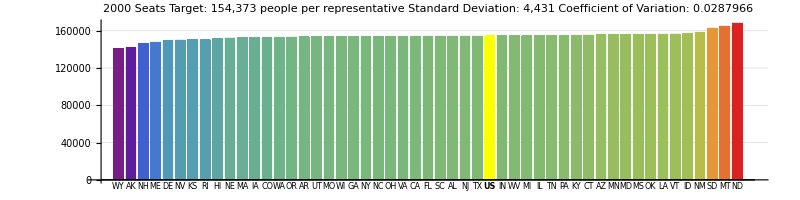

```mathematica
Get["apportionmentFunctions.m"]
```

```mathematica
apportionmentFunctions = NotebookImport["apportionmentFunctions.nb",_];
```

```mathematica
NotebookEvaluate[apportionmentFunctions];
```

```mathematica
nb = NotebookRead[apportionmentFunctions];
```

```mathematica
NotebookEvaluate[nb];
```

```mathematica
stateAbbrs50
```

stateAbbrs50